# 3. Newton Raphson

```mathematica
newtonraphson[f_,p0_,n_]:=Module[{},p1=N[p0];
i=1;
df[x_]=D[f[x],x];
Print["___________________"];
Print["Sno.","      ","Root"];
Print["___________________"];
While[i≤n,
p2=N[p1-N[f[p1]]/N[df[p1]]];
Print[i,"       ",p2];
i++;
p1=p2];
Print["Root = ",p2];
Plot[f[x],{x,1,3}]
]
```

## Question - 1

___________________

Sno.      Root

___________________

1       1.76923

2       1.73292

3       1.73205

4       1.73205

5       1.73205

Root = 1.73205

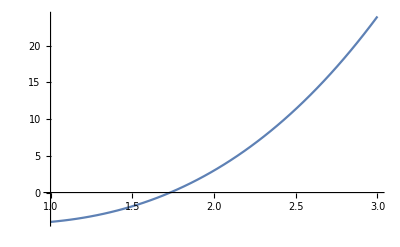

```mathematica
f[x_]:=x^3+x^2-3*x-3;
newtonraphson[f,2,5]
```

## Question -2

-1-3 x+x^3

___________________

Sno.      Root

___________________

1       -0.333333

2       -0.347222

3       -0.347296

Root = -0.347296

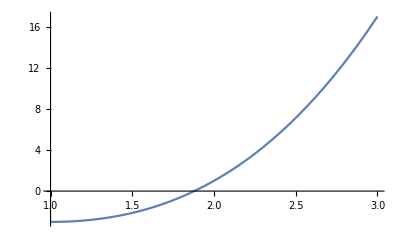

```mathematica
f[x_] = x^3-3*x-1
newtonraphson[f,0,3]
```

## Question - 3

x^2+Sin[x]

___________________

Sno.      Root

___________________

1       -5.17522

2       -2.38061

3       -1.47317

4       -1.06073

5       -0.906166

6       -0.877734

7       -0.876727

8       -0.876726

9       -0.876726

10       -0.876726

Root = -0.876726

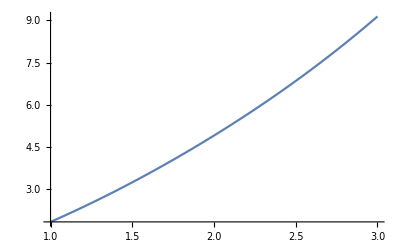

```mathematica
f[x_] = Sin[x]+x^2
newtonraphson[f,-10,10]
```

## Question - 4

x^2+x^4

___________________

Sno.      Root

___________________

1       0.666667

2       0.411765

3       0.23195

4       0.121608

5       0.0616776

6       0.0309552

7       0.0154924

8       0.00774807

9       0.00387427

10       0.00193716

Root = 0.00193716

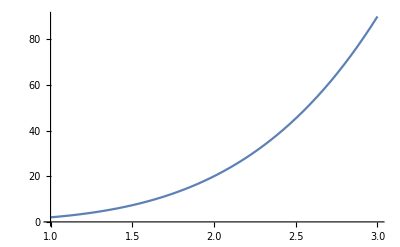

```mathematica
f[x_] = x^4+x^2
newtonraphson[f,1,10]
```